```mathematica
Quit[]
```

## Functions for rigid body transformations:

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];


Hat[r_]:=Module[{rHat},rHat={{0,-r[[3,1]],r[[2,1]]},{r[[3,1]],0,-r[[1,1]]},{-r[[2,1]],r[[1,1]],0}};
Return[rHat];]

UnHat[rHat_]:=Module[{r},r={{rHat[[3,2]]},{rHat[[1,3]]},{rHat[[2,1]]}};
Return[r];]

UnHat3D[VHat_]:=
	Module[{V},
	V=Join[UnHat[VHat[[1;;3,1;;3]]],{VHat[[1;;3,4]]}ᵀ];
		Return[V];]

Homogenize[rNonHomog_]:=
Module[{rHomog},
rHomog = Join[rNonHomog,{{1}}];
Return[rHomog];]

NonHomogenize[rHomog_]:=
Module[{rNonHomog},
rNonHomog=Drop[rHomog,-1];
Return[rNonHomog];]

InverseTransformMatrix[T_]:=
	Module[{R,p,TInv},
		R=T[[1;;3,1;;3]];
		p=T[[1;;3,4]];
		TInv=Insert[Insert[R,-Rᵀ.p,4]ᵀ,{0,0,0,1},4];
		Return[TInv];
	]
```

## Rotation of a Cuboid Impacting a Point in Space, and Going Unstable About it’s Unstable Axis As a Result (Using the Euler Lagrange Energy Method) :

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[1.17768]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17773} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[1.63311]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[1.75234]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[1.92646]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.92649} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.20369]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.20371} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.85571]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.85573} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.85828]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.85831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.86098]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.86099} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.86248]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.86248} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.86248]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.86248} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.86257]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.86257} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Return[2.8626]

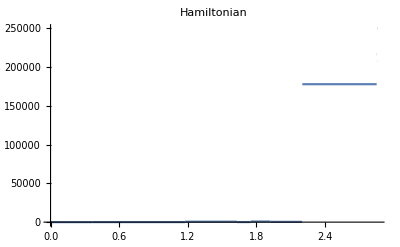

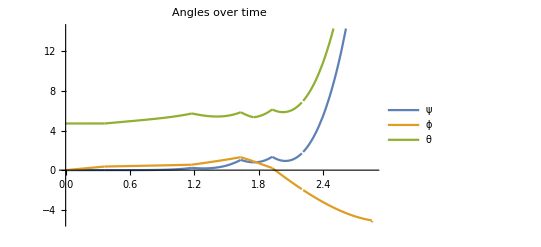

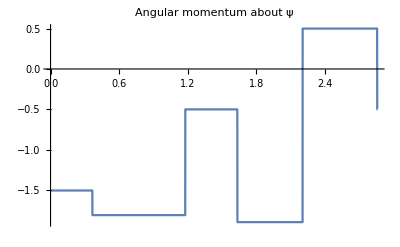

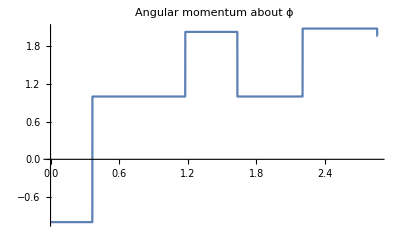

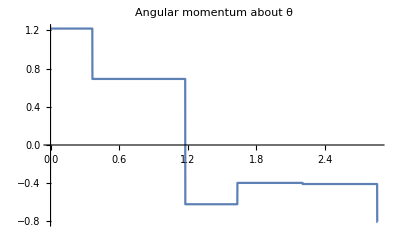

```mathematica
(*CONFIGURATION VARIABLES 3D: *)

q={{ψ[t]},{ϕ[t]},{θ[t]}};
(*FIRST AND SECOND TIME DERIVATIVES: *)
dq = D[q, t];
ddq = D[dq, t];

(*ROTATION ABOUT X AXIS: *)
ωx = {1,0,0};
Rx = RotationMatrix[ψ[t], ωx];

(*ROTATION ABOUT Y AXIS: *)
ωy = {0,1,0};
Ry = RotationMatrix[ϕ[t], ωy];

(*ROTATION ABOUT Z AXIS: *)
ωz = {0,0,1};
Rz = RotationMatrix[θ[t], ωz];

R = Rx.Ry.Rz;

p = {{0},{0},{0}};
Twb = Join[Join[Rᵀ,pᵀ]ᵀ, {{0,0,0,1}}];
Twbdot = D[Twb, t];

Tbw = InverseTransformMatrix[Twb];

(*BODY VELOCITIES: *)
V= UnHat3D[Inverse[Twb].Twbdot];

(*Intertia Tensors*)
rb={{x},{y},{z}};
rhat = Hat[rb];
ℐ =∫_(-zd/2)^(zd/2) ∫_(-yd/2)^(yd/2) ∫_(-xd/2)^(xd/2) ρ*( rhat)ᵀ.( rhat )ⅆxⅆyⅆz;

G = Join[Join[m*IdentityMatrix[3],ConstantArray[0,{3,3}]]ᵀ, Join[ConstantArray[0,{3,3}],ℐ]ᵀ];

(*KINETIC ENERGY: *)
KE = 1/2*Vᵀ.G.V;

(*TODO::: FIX INERTIAL FRAME: *)
CM =  {{0},{0},{0}};
rW = NonHomogenize[Twb.Homogenize[CM]];

(*POTENTIAL ENERGY: *)
PE = m*g*rW[[3]];

(*LAGRANGIAN: *)
Lag = KE - PE//FullSimplify;
(*Generalized momentum*)
p = D[Lag, dqᵀ];

(*Hamiltonian*)
TotalEnergy = KE + PE;
Ham = p.dq-Lag;

(*EULER LAGRANGE EQUATIONS: *)
Eq1 = D[D[Lag, dq[[1]]],t]-D[Lag, q[[1]]] ==0;
Eq2 = D[D[Lag, dq[[2]]],t]-D[Lag, q[[2]]] ==0;
Eq3 = D[D[Lag, dq[[3]]],t]-D[Lag, q[[3]]] == 0;

(*FIND EQUTIONS OF MOTION: *)
ELtemp = Solve[Eq1&& Eq2 && Eq3,Flatten[{ddq}]];

(*PARAMETERS: *)
m=10;xd=1;yd=2;zd=3;g=9.81;ρ = 3;

(*INITIAL CONDITIONS: *)
InitCon= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.005,
Derivative[1][ϕ][0]==1,
Derivative[1][θ][0]==0.005};

(*IMPACTS: *)
(*Point of Impact in Space: *)
pw={{-xd/2},{yd/2+yd/4},{zd/2}};
pb=Tbw.Homogenize[pw];

(*IMPACT CONDITIONS: *)
phi1impact=pb[[1]]-xd/2;
phi2impact=pb[[1]]+xd/2;
phi3impact = pb[[2]]-yd/2;
phi4impact = pb[[2]] +yd/2;
phi5impact = pb[[3]]-zd/2;
phi6impact = pb[[3]]+zd/2;

gradphi1impact = D[phi1impact,qᵀ];
gradphi2impact = D[phi2impact,qᵀ];
gradphi3impact = D[phi3impact,qᵀ];
gradphi4impact = D[phi4impact,qᵀ];
gradphi5impact = D[phi5impact,qᵀ];
gradphi6impact = D[phi6impact,qᵀ];

EL={ψ''[t]==ELtemp[[1,1,2]],ϕ''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};
tmax = 10;

(*FINDING FIRST IMPACT :*)
(****************************************************************************************)
Impsol1 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi4impact }];
tmax1 = InterpolatingFunctionDomain[First[ψ/.Impsol1]][[1,-1]];

pbsol1=(pb/.t-> tmax1)/.Impsol1[[1]];
Twbsol1 =( Tbw/.t-> tmax1)/.Impsol1[[1]];
pwsol1 =NonHomogenize[Twbsol1.Homogenize[pw]];

(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus;
Hamold1 = ((Hamminus/.tminus-> tmax1)/.Impsol1)[[1]];
Hamplus1 = (Ham/.t-> tplus)/.{ψ[tplus]-> (ψ[tmax1]/.Impsol1)[[1]], ϕ[tplus]-> (ϕ[tmax1]/.Impsol1)[[1]],θ[tplus]-> (θ[tmax1]/.Impsol1)[[1]]};

pminus = p/.t-> tminus;
pold = ((pminus/.tminus-> tmax1)/.Impsol1)[[1]]//FullSimplify;
pplus = (p/.t-> tplus)/.{ψ[tplus]-> (ψ[tmax1]/.Impsol1)[[1]], ϕ[tplus]-> (ϕ[tmax1]/.Impsol1)[[1]],θ[tplus]-> (θ[tmax1]/.Impsol1)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi4impact =(( gradphi4impact/.t->  tmax1)/.Impsol1)[[1]];
qprimupdate = Solve[Hamplus1-Hamold1 == 0 && pplus-pold== λ*{gradphi4impact},Flatten[{ψ'[tplus],ϕ'[tplus],θ'[tplus],λ}]];
(****************************************************************************************)
tmax2 = 10;

ϵ = 10^(-6);
(*FINDING SECOND IMPACT :*)
(****************************************************************************************)
If[Abs[λ/.qprimupdate[[1,4]]]<ϵ,
Impsol2=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax2 = InterpolatingFunctionDomain[First[ψ/.Impsol2]][[1,-1]];
(*Print["tmax 2 using second labmda first loop:   ", tmax2];*)
Return[tmax2]]

If[Abs[λ/.qprimupdate[[2,4]]]<ϵ,
Impsol2=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[1,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[1,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[1,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax2 = InterpolatingFunctionDomain[First[ψ/.Impsol2]][[1,-1]];
(*Print["tmax2 using first lambda second loop: ", tmax2]*)
Return[tmax2]]

(*IMPACT UPDATE EQATIONS:*)
pbsol2=(pb/.t-> tmax2)/.Impsol2[[1]];
Twbsol2 =( Tbw/.t-> tmax2)/.Impsol2[[1]];
pwsol2 =NonHomogenize[Twbsol2.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus2;
Hamold2 = ((Hamminus/.tminus2-> tmax2)/.Impsol2)[[1]];
Hamplus2 = (Ham/.t-> tplus2)/.{ψ[tplus2]-> (ψ[tmax2]/.Impsol2)[[1]], ϕ[tplus2]-> (ϕ[tmax2]/.Impsol2)[[1]],θ[tplus2]-> (θ[tmax2]/.Impsol2)[[1]]};

pminus = p/.t-> tminus2;
pold = ((pminus/.tminus2-> tmax2)/.Impsol2)[[1]]//FullSimplify;
pplus = (p/.t-> tplus2)/.{ψ[tplus2]-> (ψ[tmax2]/.Impsol2)[[1]], ϕ[tplus2]-> (ϕ[tmax2]/.Impsol2)[[1]],θ[tplus2]-> (θ[tmax2]/.Impsol2)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax2)/.Impsol2)[[1]];
qprimupdate2 = Solve[Hamplus2-Hamold2 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus2],ϕ'[tplus2],θ'[tplus2],λ}]];

(***********************************************************************************************)

tmax3 = 10;
(*FINDING THIRD IMPACT :*)
(****************************************************************************************)
If[Abs[λ/.qprimupdate2[[1,4]]]<ϵ,
Impsol3=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[2,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax3 = InterpolatingFunctionDomain[First[ψ/.Impsol3]][[1,-1]];
(*Print["tmax 3 using second lambda first loop: ", tmax3];*)
Return[tmax3]]

If[Abs[λ/.qprimupdate2[[2,4]]]<ϵ,
Impsol3=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[1,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[1,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax3 = InterpolatingFunctionDomain[First[ψ/.Impsol3]][[1,-1]];
(*Print["tmax 3 using first lambda second loop", tmax3];*)
Return[tmax3]]

pbsol3=(pb/.t-> tmax3)/.Impsol3[[1]];
Twbsol3 =( Tbw/.t-> tmax3)/.Impsol3[[1]];
pwsol3 =NonHomogenize[Twbsol3.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus3;
Hamold3 = ((Hamminus/.tminus3-> tmax3)/.Impsol3)[[1]];
Hamplus3 = (Ham/.t-> tplus3)/.{ψ[tplus3]-> (ψ[tmax3]/.Impsol3)[[1]], ϕ[tplus3]-> (ϕ[tmax3]/.Impsol3)[[1]],θ[tplus3]-> (θ[tmax3]/.Impsol3)[[1]]};

pminus = p/.t-> tminus3;
pold = ((pminus/.tminus3-> tmax3)/.Impsol3)[[1]]//FullSimplify;
pplus = (p/.t-> tplus3)/.{ψ[tplus3]-> (ψ[tmax3]/.Impsol3)[[1]], ϕ[tplus3]-> (ϕ[tmax3]/.Impsol3)[[1]],θ[tplus3]-> (θ[tmax3]/.Impsol3)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax3)/.Impsol3)[[1]];
qprimupdate3 = Solve[Hamplus3-Hamold3 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus3],ϕ'[tplus3],θ'[tplus3],λ}]];
(****************************************************************************************)
tmax4 = 10;

(*Finding fourth impact: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate3[[1,4]]]<ϵ,
Impsol4=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[2,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[2,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[2,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax4 = InterpolatingFunctionDomain[First[ψ/.Impsol4]][[1,-1]];
(*Print["tmax 4 using second lambda first loop: ", tmax4];*)
Return[tmax4]]

If[Abs[λ/.qprimupdate3[[2,4]]]<ϵ,
Impsol4=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax4 = InterpolatingFunctionDomain[First[ψ/.Impsol4]][[1,-1]];
(*Print["tmax 4 using first lambda second loop", tmax4];*)
Return[tmax4]]

pbsol4=(pb/.t-> tmax4)/.Impsol4[[1]];
Twbsol4 =( Tbw/.t-> tmax4)/.Impsol4[[1]];
pwsol4 =NonHomogenize[Twbsol4.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus4;
Hamold4 = ((Hamminus/.tminus4-> tmax4)/.Impsol4)[[1]];
Hamplus4 = (Ham/.t-> tplus4)/.{ψ[tplus4]-> (ψ[tmax4]/.Impsol4)[[1]], ϕ[tplus4]-> (ϕ[tmax4]/.Impsol4)[[1]],θ[tplus4]-> (θ[tmax4]/.Impsol4)[[1]]};

pminus = p/.t-> tminus4;
pold = ((pminus/.tminus4-> tmax4)/.Impsol4)[[1]]//FullSimplify;
pplus = (p/.t-> tplus4)/.{ψ[tplus4]-> (ψ[tmax4]/.Impsol4)[[1]], ϕ[tplus4]-> (ϕ[tmax4]/.Impsol4)[[1]],θ[tplus4]-> (θ[tmax4]/.Impsol4)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax4)/.Impsol4)[[1]];
qprimupdate4 = Solve[Hamplus4-Hamold4 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus4],ϕ'[tplus4],θ'[tplus4],λ}]];
(**************************************************************************************)
tmax5 = 10;

(*FINDING FIFTH IMAPCT: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate4[[1,4]]]<ϵ,

Impsol5=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax5 = InterpolatingFunctionDomain[First[ψ/.Impsol5]][[1,-1]];
(*Print["tmax 5 using second lambda first loop: ", tmax5];*)
Return[tmax5]]

If[Abs[λ/.qprimupdate4[[2,4]]]<ϵ,
Impsol5=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[1,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[1,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[1,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax5 = InterpolatingFunctionDomain[First[ψ/.Impsol5]][[-1,1]];
(*Print["tmax 5 using first lambda second loop", tmax5];*)
Return[tmax5]]

pbsol5 =(pb/.t-> tmax4)/.Impsol4[[1]];
Twbsol5 =( Tbw/.t-> tmax5)/.Impsol5[[1]];
pwsol5 =NonHomogenize[Twbsol5.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus5;
Hamold5 = ((Hamminus/.tminus5-> tmax5)/.Impsol5)[[1]];
Hamplus5 = (Ham/.t-> tplus5)/.{ψ[tplus5]-> (ψ[tmax5]/.Impsol5)[[1]], ϕ[tplus5]-> (ϕ[tmax5]/.Impsol5)[[1]],θ[tplus5]-> (θ[tmax5]/.Impsol5)[[1]]};

pminus = p/.t-> tminus5;
pold = ((pminus/.tminus5-> tmax5)/.Impsol5)[[1]]//FullSimplify;
pplus = (p/.t-> tplus5)/.{ψ[tplus5]-> (ψ[tmax5]/.Impsol5)[[1]], ϕ[tplus5]-> (ϕ[tmax5]/.Impsol5)[[1]],θ[tplus5]-> (θ[tmax5]/.Impsol5)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax5)/.Impsol5)[[1]];
qprimupdate5 = Solve[Hamplus5-Hamold5 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus5],ϕ'[tplus5],θ'[tplus5],λ}]];
(****************************************************************************************)

tmax6 = 10;
(*Finding for sixth impact: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate5[[1,4]]]<ϵ,
Impsol6=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[2,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[2,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[2,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax6 = InterpolatingFunctionDomain[First[ψ/.Impsol6]][[1,-1]];
Print["tmax 6 using second lambda first loop: ", tmax6];
Return[tmax6]]

If[Abs[λ/.qprimupdate5[[2,4]]]<ϵ,
Impsol6=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax6 = InterpolatingFunctionDomain[First[ψ/.Impsol6]][[1,-1]];
(*Print["tmax 6 using second lambda first loop: ", tmax6];*)
Return[tmax6]]

pbsol6 =(pb/.t-> tmax4)/.Impsol4[[1]];
Twbsol6 =( Tbw/.t-> tmax6)/.Impsol6[[1]];
pwsol6 =NonHomogenize[Twbsol6.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus6;
Hamold6 = ((Hamminus/.tminus6-> tmax6)/.Impsol6)[[1]];
Hamplus6 = (Ham/.t-> tplus6)/.{ψ[tplus6]-> (ψ[tmax6]/.Impsol6)[[1]], ϕ[tplus6]-> (ϕ[tmax6]/.Impsol6)[[1]],θ[tplus6]-> (θ[tmax6]/.Impsol6)[[1]]};

pminus = p/.t-> tminus6;
pold = ((pminus/.tminus6-> tmax6)/.Impsol6)[[1]]//FullSimplify;
pplus = (p/.t-> tplus6)/.{ψ[tplus6]-> (ψ[tmax6]/.Impsol6)[[1]], ϕ[tplus6]-> (ϕ[tmax6]/.Impsol6)[[1]],θ[tplus6]-> (θ[tmax6]/.Impsol6)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax6)/.Impsol6)[[1]];
qprimupdate6 = Solve[Hamplus6-Hamold6 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus6],ϕ'[tplus6],θ'[tplus6],λ}]];
(****************************************************************************************)

tmax7 = 10;
(*Finding for seventh impact: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate6[[1,4]]]<ϵ,
Impsol7=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax7 = InterpolatingFunctionDomain[First[ψ/.Impsol7]][[1,-1]];
(*Print["tmax 7 using second lambda first loop: ", tmax7];*)
Return[tmax7]]

If[Abs[λ/.qprimupdate6[[2,4]]]<ϵ,
Impsol7=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[2,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[2,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[2,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax7 = InterpolatingFunctionDomain[First[ψ/.Impsol7]][[1,-1]];
(*Print["tmax 7 using second lambda first loop: ", tmax7];*)
Return[tmax7]]

pbsol7= (pb/.t-> tmax7)/.Impsol7[[1]];
Twbsol7 =( Tbw/.t-> tmax7)/.Impsol7[[1]];
pwsol7 =NonHomogenize[Twbsol7.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus7;
Hamold7 = ((Hamminus/.tminus7-> tmax7)/.Impsol7)[[1]];
Hamplus7 = (Ham/.t-> tplus7)/.{ψ[tplus7]-> (ψ[tmax7]/.Impsol7)[[1]], ϕ[tplus7]-> (ϕ[tmax7]/.Impsol7)[[1]],θ[tplus7]-> (θ[tmax7]/.Impsol7)[[1]]};

pminus = p/.t-> tminus7;
pold = ((pminus/.tminus7-> tmax7)/.Impsol7)[[1]]//FullSimplify;
pplus = (p/.t-> tplus7)/.{ψ[tplus7]-> (ψ[tmax7]/.Impsol7)[[1]], ϕ[tplus7]-> (ϕ[tmax7]/.Impsol7)[[1]],θ[tplus7]-> (θ[tmax7]/.Impsol7)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax7)/.Impsol7)[[1]];
qprimupdate7 = Solve[Hamplus7-Hamold7 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus7],ϕ'[tplus7],θ'[tplus7],λ}]];
(****************************************************************************************)

tmax8=10;
(*Finding eighth impact: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate7[[1,4]]]<ϵ,
Impsol8=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax8 = InterpolatingFunctionDomain[First[ψ/.Impsol8]][[1,-1]];
(*Print["tmax 8 using second lambda first loop: ", tmax8];*)
Return[tmax8]]

If[Abs[λ/.qprimupdate7[[2,4]]]<ϵ,
Impsol8=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[1,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[1,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[1,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax8 = InterpolatingFunctionDomain[First[ψ/.Impsol8]][[1,-1]];
(*Print["tmax 8 using second lambda first loop: ", tmax8];*)
Return[tmax8]]

pbsol8=(pb/.t-> tmax8)/.Impsol8[[1]];
Twbsol8 =( Tbw/.t-> tmax8)/.Impsol8[[1]];
pwsol8 =NonHomogenize[Twbsol8.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus8;
Hamold8 = ((Hamminus/.tminus8-> tmax8)/.Impsol8)[[1]];
Hamplus8 = (Ham/.t-> tplus8)/.{ψ[tplus8]-> (ψ[tmax8]/.Impsol8)[[1]], ϕ[tplus8]-> (ϕ[tmax8]/.Impsol8)[[1]],θ[tplus8]-> (θ[tmax8]/.Impsol8)[[1]]};

pminus = p/.t-> tminus8;
pold = ((pminus/.tminus8-> tmax8)/.Impsol8)[[1]]//FullSimplify;
pplus = (p/.t-> tplus8)/.{ψ[tplus8]-> (ψ[tmax8]/.Impsol8)[[1]], ϕ[tplus8]-> (ϕ[tmax8]/.Impsol8)[[1]],θ[tplus8]-> (θ[tmax8]/.Impsol8)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax8)/.Impsol8)[[1]];
qprimupdate8 = Solve[Hamplus8-Hamold8 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus8],ϕ'[tplus8],θ'[tplus8],λ}]];
(****************************************************************************************)

tmax9=10;
(*Finding ninth impact: *)
(****************************************************************************************)
If[Abs[λ/.qprimupdate8[[1,4]]]<ϵ,
Impsol9=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax9 = InterpolatingFunctionDomain[First[ψ/.Impsol9]][[1,-1]];
(*Print["tmax 9 using second lambda first loop: ", tmax9];*)
Return[tmax9]]

If[Abs[λ/.qprimupdate8[[2,4]]]<ϵ,
Impsol9=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[1,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[1,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[1,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax9 = InterpolatingFunctionDomain[First[ψ/.Impsol9]][[1,-1]];
(*Print["tmax 9 using second lambda first loop: ", tmax9];*)
Return[tmax9]]
pbsol9=(pb/.t-> tmax9)/.Impsol9[[1]];
Twbsol9 =( Tbw/.t-> tmax9)/.Impsol9[[1]];
pwsol9 =NonHomogenize[Twbsol9.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus9;
Hamold9 = ((Hamminus/.tminus9-> tmax9)/.Impsol9)[[1]];
Hamplus9 = (Ham/.t-> tplus9)/.{ψ[tplus9]-> (ψ[tmax9]/.Impsol9)[[1]], ϕ[tplus9]-> (ϕ[tmax9]/.Impsol9)[[1]],θ[tplus9]-> (θ[tmax9]/.Impsol9)[[1]]};

pminus = p/.t-> tminus9;
pold = ((pminus/.tminus9-> tmax9)/.Impsol9)[[1]]//FullSimplify;
pplus = (p/.t-> tplus9)/.{ψ[tplus9]-> (ψ[tmax9]/.Impsol9)[[1]], ϕ[tplus9]-> (ϕ[tmax9]/.Impsol9)[[1]],θ[tplus9]-> (θ[tmax9]/.Impsol9)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax9)/.Impsol9)[[1]];
qprimupdate9 = Solve[Hamplus9-Hamold9 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus9],ϕ'[tplus9],θ'[tplus9],λ}]];
(****************************************************************************************)

(*Finding tenth impact: *)
tmax10 = 10;
(****************************************************************************************)
If[Abs[λ/.qprimupdate9[[1,4]]]<ϵ,
Impsol10=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[2,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[2,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[2,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi6impact)}];

tmax10 = InterpolatingFunctionDomain[First[ψ/.Impsol10]][[1,-1]];
(*Print["tmax 10 using second lambda first loop: ", tmax10];*)
Return[tmax10]]

If[Abs[λ/.qprimupdate9[[2,4]]]<ϵ,
Impsol10=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax10 = InterpolatingFunctionDomain[First[ψ/.Impsol10]][[1,-1]];
(*Print["tmax 10 using second lambda first loop: ", tmax10];*)
Return[tmax10]]
pbsol10=(pb/.t-> tmax10)/.Impsol10[[1]];
Twbsol10 =( Tbw/.t-> tmax10)/.Impsol10[[1]];
pwsol10 =NonHomogenize[Twbsol10.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus10;
Hamold10 = ((Hamminus/.tminus10-> tmax10)/.Impsol10)[[1]];
Hamplus10 = (Ham/.t-> tplus10)/.{ψ[tplus10]-> (ψ[tmax10]/.Impsol10)[[1]], ϕ[tplus10]-> (ϕ[tmax10]/.Impsol10)[[1]],θ[tplus10]-> (θ[tmax10]/.Impsol10)[[1]]};

pminus = p/.t-> tminus10;
pold = ((pminus/.tminus10-> tmax10)/.Impsol10)[[1]]//FullSimplify;
pplus = (p/.t-> tplus10)/.{ψ[tplus10]-> (ψ[tmax10]/.Impsol10)[[1]], ϕ[tplus10]-> (ϕ[tmax10]/.Impsol10)[[1]],θ[tplus10]-> (θ[tmax10]/.Impsol10)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax10)/.Impsol10)[[1]];
qprimupdate10 = Solve[Hamplus10-Hamold10 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus10],ϕ'[tplus10],θ'[tplus10],λ}]];
(****************************************************************************************)

(*finding for tmax11 :*)
(****************************************************************************************)
tmax11=10;

If[Abs[λ/.qprimupdate10[[1,4]]]<ϵ,
Impsol11= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[2,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[2,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[2,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi6impact)}];

tmax11 = InterpolatingFunctionDomain[First[ψ/.Impsol11]][[1,-1]];
(*Print["tmax 11 using second lambda first loop: ", tmax11];*)
Return[tmax11]]

If[Abs[λ/.qprimupdate10[[2,4]]]<ϵ,
Impsol11= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi6impact)}];

tmax11 = InterpolatingFunctionDomain[First[ψ/.Impsol11]][[1,-1]];
(*Print["tmax 11 using second lambda first loop: ", tmax11];*)
Return[tmax11]]
pbsol11=(pb/.t-> tmax11)/.Impsol11[[1]];
Twbsol11 =( Tbw/.t-> tmax11)/.Impsol11[[1]];
pwsol11 =NonHomogenize[Twbsol11.Homogenize[pw]];
(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus11;
Hamold11 = ((Hamminus/.tminus11-> tmax11)/.Impsol11)[[1]];
Hamplus11= (Ham/.t-> tplus11)/.{ψ[tplus11]-> (ψ[tmax11]/.Impsol11)[[1]], ϕ[tplus11]-> (ϕ[tmax11]/.Impsol11)[[1]],θ[tplus11]-> (θ[tmax11]/.Impsol11)[[1]]};

pminus = p/.t-> tminus11;
pold = ((pminus/.tminus11-> tmax11)/.Impsol11)[[1]]//FullSimplify;
pplus = (p/.t-> tplus11)/.{ψ[tplus11]-> (ψ[tmax11]/.Impsol11)[[1]], ϕ[tplus11]-> (ϕ[tmax11]/.Impsol11)[[1]],θ[tplus11]-> (θ[tmax11]/.Impsol11)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi6impact =(( gradphi6impact/.t->  tmax11)/.Impsol11)[[1]];
qprimupdate11 = Solve[Hamplus11-Hamold11 == 0 && pplus-pold== λ*{gradphi6impact},Flatten[{ψ'[tplus11],ϕ'[tplus11],θ'[tplus11],λ}]];
(****************************************************************************************)

(*Finding twelfth impact: *)
(****************************************************************************************)
tmax12=10;

If[Abs[λ/.qprimupdate11[[1,4]]]<ϵ,
Impsol12= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[2,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[2,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[2,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax12 = InterpolatingFunctionDomain[First[ψ/.Impsol12]][[1,-1]];
(*Print["tmax 12 using second lambda first loop: ", tmax12];*)
Return[tmax12]]

If[Abs[λ/.qprimupdate11[[2,4]]]<ϵ,
Impsol12= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax12 = InterpolatingFunctionDomain[First[ψ/.Impsol12]][[1,-1]];
(*Print["tmax 12 using second lambda first loop: ", tmax12];*)
Return[tmax12]]

pbsol12=(pb/.t-> tmax12)/.Impsol12[[1]];
Twbsol12 =( Tbw/.t-> tmax12)/.Impsol12[[1]];
pwsol12 =NonHomogenize[Twbsol12.Homogenize[pw]];

(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus12;
Hamold12 = ((Hamminus/.tminus12-> tmax12)/.Impsol12)[[1]];
Hamplus12 = (Ham/.t-> tplus12)/.{ψ[tplus12]-> (ψ[tmax12]/.Impsol12)[[1]], ϕ[tplus12]-> (ϕ[tmax12]/.Impsol12)[[1]],θ[tplus12]-> (θ[tmax12]/.Impsol12)[[1]]};

pminus = p/.t-> tminus12;
pold = ((pminus/.tminus12-> tmax12)/.Impsol12)[[1]]//FullSimplify;
pplus = (p/.t-> tplus12)/.{ψ[tplus12]-> (ψ[tmax12]/.Impsol12)[[1]], ϕ[tplus12]-> (ϕ[tmax12]/.Impsol12)[[1]],θ[tplus12]-> (θ[tmax12]/.Impsol12)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax11)/.Impsol11)[[1]];
qprimupdate12 = Solve[Hamplus12-Hamold12 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus12],ϕ'[tplus12],θ'[tplus12],λ}]];
(****************************************************************************************)

(*Finding thirteenth time of impact: *)
tmax13 = 10;
(****************************************************************************************)
If[Abs[λ/.qprimupdate12[[1,4]]]<ϵ,
Impsol13= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax13 = InterpolatingFunctionDomain[First[ψ/.Impsol13]][[1,-1]];
Twbsol13 =( Tbw/.t-> tmax13)/.Impsol13[[1]];
pwsol13 =NonHomogenize[Twbsol13.Homogenize[pw]];
(*Print["tmax 13 using second lambda first loop: ", tmax13];*)
Return[tmax13]]

If[Abs[λ/.qprimupdate12[[2,4]]]<ϵ,
Impsol13=  NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[1,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[1,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[1,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax13 = InterpolatingFunctionDomain[First[ψ/.Impsol13]][[1,-1]];
(*Print["tmax 13 using second lambda first loop: ", tmax13];*)
Return[tmax13]]
pbsol13=(pb/.t-> tmax13)/.Impsol13[[1]];
Hamminus = Ham/.t-> tminus13;
Hamold13 = ((Hamminus/.tminus13-> tmax13)/.Impsol13)[[1]];
(******************************** PLOTS AND ANIMATION: ***************************************)

Ψ[t_]:= Piecewise[{{(ψ[t]/.Impsol1)[[1]],t<tmax1},{(ψ[t]/.Impsol2)[[1]],tmax1≤ t< tmax2},{(ψ[t]/.Impsol3)[[1]],tmax2≤ t< tmax3},{(ψ[t]/.Impsol4)[[1]],tmax3≤ t< tmax4},{(ψ[t]/.Impsol5)[[1]],tmax4≤ t< tmax5},{(ψ[t]/.Impsol6)[[1]],tmax5≤ t< tmax6},{(ψ[t]/.Impsol7)[[1]],tmax6≤ t< tmax7},{(ψ[t]/.Impsol8)[[1]],tmax7≤ t< tmax8},{(ψ[t]/.Impsol9)[[1]],tmax8≤ t< tmax9},{(ψ[t]/.Impsol10)[[1]],tmax9≤ t< tmax10},{(ψ[t]/.Impsol11)[[1]],tmax10≤ t< tmax11},{(ψ[t]/.Impsol12)[[1]],tmax11≤ t< tmax12},{(ψ[t]/.Impsol13)[[1]],tmax12≤ t< tmax13}}]
Φ[t_]:= Piecewise[{{(ϕ[t]/.Impsol1)[[1]],t<tmax1},{(ϕ[t]/.Impsol2)[[1]],tmax1≤ t< tmax2},{(ϕ[t]/.Impsol3)[[1]],tmax2≤ t< tmax3},{(ϕ[t]/.Impsol4)[[1]],tmax3≤ t< tmax4},{(ϕ[t]/.Impsol5)[[1]],tmax4≤ t< tmax5},{(ϕ[t]/.Impsol6)[[1]],tmax5≤ t< tmax6},{(ϕ[t]/.Impsol7)[[1]],tmax6≤ t< tmax7},{(ϕ[t]/.Impsol8)[[1]],tmax7≤ t< tmax8},{(ϕ[t]/.Impsol9)[[1]],tmax8≤ t< tmax9},{(ϕ[t]/.Impsol10)[[1]],tmax9≤ t< tmax10},{(ϕ[t]/.Impsol11)[[1]],tmax10≤ t< tmax11},{(ϕ[t]/.Impsol12)[[1]],tmax11≤ t< tmax12},{(ϕ[t]/.Impsol13)[[1]],tmax12≤ t< tmax13}}]
Θ[t_]:= Piecewise[{{(θ[t]/.Impsol1)[[1]],t<tmax1},{(θ[t]/.Impsol2)[[1]],tmax1≤ t< tmax2},{(θ[t]/.Impsol3)[[1]],tmax2≤ t< tmax3},{(θ[t]/.Impsol4)[[1]],tmax3≤ t< tmax4},{(θ[t]/.Impsol5)[[1]],tmax4≤ t< tmax5},{(θ[t]/.Impsol6)[[1]],tmax5≤ t< tmax6},{(θ[t]/.Impsol7)[[1]],tmax6≤ t< tmax7},{(θ[t]/.Impsol8)[[1]],tmax7≤ t< tmax8},{(θ[t]/.Impsol9)[[1]],tmax8≤ t< tmax9},{(θ[t]/.Impsol10)[[1]],tmax9≤ t< tmax10},{(θ[t]/.Impsol11)[[1]],tmax10≤ t< tmax11},{(θ[t]/.Impsol12)[[1]],tmax11≤ t< tmax12},{(θ[t]/.Impsol13)[[1]],tmax12≤ t< tmax13}}]
Ham= Piecewise[{{
{Hamold1[[1,1,1]]},0<t<tmax1},{{Hamold2[[1,1,1]]},tmax1≤ t< tmax2},{{Hamold3[[1,1,1]]},tmax2≤ t< tmax3},{{Hamold4[[1,1,1]]},tmax3≤ t< tmax4},{{Hamold5[[1,1,1]]},tmax4≤ t< tmax5},{{Hamold6[[1,1,1]]},tmax5≤ t< tmax6},{{Hamold7[[1,1,1]]},tmax6≤ t< tmax7},{{Hamold8[[1,1,1]]},tmax7≤ t< tmax8},{{Hamold9[[1,1,1]]},tmax8≤ t< tmax9},{{Hamold10[[1,1,1]]},tmax9≤ t< tmax10},{{Hamold11[[1,1,1]]},tmax10≤ t< tmax11},{{Hamold11[[1,1,1]]},tmax10≤ t< tmax12}}];
point[t_] :=  Piecewise[{{
{pwsol1},0<t<tmax1},{{pwsol2},tmax1≤ t< tmax2},{{pwsol3},tmax2≤ t< tmax3},{{pwsol4},tmax3≤ t< tmax4},{{pwsol5},tmax4≤ t< tmax5},{{pwsol6},tmax5≤ t< tmax6},{{pwsol7},tmax6≤ t< tmax7},{{pwsol8},tmax7≤ t< tmax8},{{pwsol9},tmax8≤ t< tmax9},{{pwsol10},tmax9≤ t< tmax10},{{pwsol11},tmax10≤ t< tmax11},{{pwsol12},tmax11≤ t< tmax12},{{pwsol13},tmax12≤ t< tmax13}}];
pbsol[t_] :=  Piecewise[{{pbsol1, t<tmax1},{pbsol2,tmax1≤ t< tmax2},{pbsol3,tmax2≤ t< tmax3},{pbsol4,tmax3≤ t< tmax4},{pbsol5,tmax4≤ t< tmax5},{pbsol6,tmax5≤ t< tmax6},{pbsol7,tmax6≤ t< tmax7},{pbsol8,tmax7≤ t< tmax8},{pbsol9,tmax8≤ t< tmax9},{pbsol10,tmax9≤ t< tmax10},{pbsol11,tmax10≤ t< tmax11},{pbsol12,tmax11≤ t< tmax12},{pbsol13,tmax12≤ t< tmax13}}];
Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},Ψ[τ],{1,0,0}],Φ[τ],{0,1,0}],Θ[τ],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Cuboid rotating about y-axis with an intial velocity of ψ=1, impacing a point with coordinates:{{-0.5},{0.75},{1.5}}"],{τ,0,tmax13}, AnimationRate->.5]

Plot[Ham,{t,0,tmax12}, PlotLabel->"Hamiltonian"]
Plot[{Ψ[t],Φ[t],Θ[t]},{t,0,tmax13}, PlotLegends->{"ψ","ϕ","θ"},PlotLabel->"Angles over time"]
Plot[pbsol[t][[1]],{t,0,tmax8},PlotLabel->"Angular momentum about ψ"]
Plot[pbsol[t][[2]],{t,0,tmax8},PlotLabel->"Angular momentum about ϕ"]
Plot[pbsol[t][[3]],{t,0,tmax8},PlotLabel->"Angular momentum about θ"]
```

## Rotation about a set of principle axis (Using the Euler Lagrange Energy Method -NO IMPACTS):

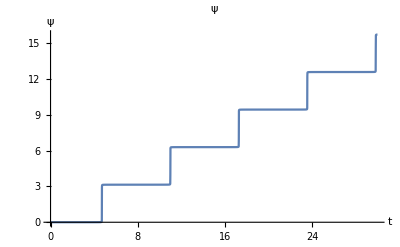

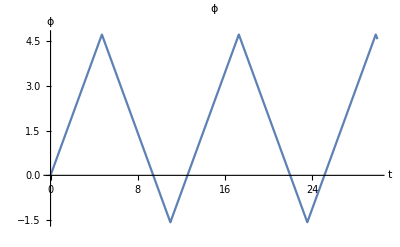

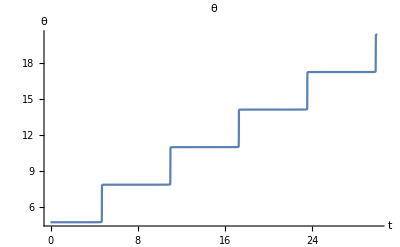

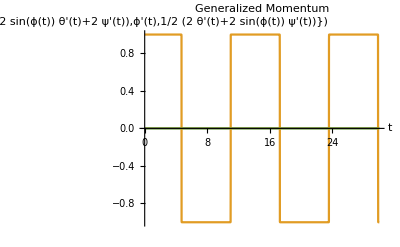

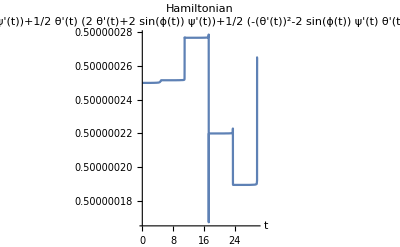

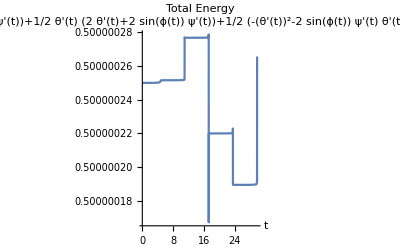

```mathematica
(*CONFIGURATION VARIABLES 3D: *)
q={{ψ[t]},{ϕ[t]},{θ[t]}};
(*FIRST AND SECOND TIME DERIVATIVES: *)
dq = D[q, t];
ddq = D[dq, t];

(*ROTATION ABOUT X AXIS: *)
ωx = {1,0,0};
Rx = RotationMatrix[ψ[t], ωx];

(*ROTATION ABOUT Y AXIS: *)
ωy = {0,1,0};
Ry = RotationMatrix[ϕ[t], ωy];

(*ROTATION ABOUT Z AXIS: *)
ωz = {0,0,1};
Rz = RotationMatrix[θ[t], ωz];

R = Rx.Ry.Rz;
(*p = {{x[t]},{y[t]},{z[t]}};*)
p = {{0},{0},{0}};
T = Join[Join[Rᵀ,pᵀ]ᵀ, {{0,0,0,1}}];
Tdot = D[T, t];

(*BODY VELOCITIES: *)
V= UnHat3D[Inverse[T].Tdot];

(*Intertia Tensors*)
Ix=(1/12)*m*(yd^2+zd^2);
Iy=(1/12)*m*(zd^2+xd^2);
Iz=(1/12)*m*(xd^2+yd^2);
ℐ= {{Ix, 0, 0},{0, Iy, 0},{0,0, Iz}};
(*TO DO ::: ROTATIONAL INERTIA*)
(*
rb={{x},{y},{z}};
rhat = Hat[rb];
ℐ =∫_(-zd/2)^(zd/2) ∫_(-yd/2)^(yd/2) ∫_(-xd/2)^(xd/2) ρ*( rhat)ᵀ.( rhat )ⅆxⅆyⅆz;*)

G = Join[Join[m*IdentityMatrix[3],ConstantArray[0,{3,3}]]ᵀ, Join[ConstantArray[0,{3,3}],ℐ]ᵀ];

(*KINETIC ENERGY: *)
KE = 1/2*Vᵀ.G.V;

(*TODO::: FIX INERTIAL FRAME: *)
CM =  {{0},{0},{0}};
rW = NonHomogenize[T.Homogenize[CM]];

(*POTENTIAL ENERGY: *)
PE = m*g*rW[[3]];

(*LAGRANGIAN: *)
Lag = KE - PE//FullSimplify;
(*Generalized momentum*)
p = D[Lag, dqᵀ];

(*Hamiltonian*)
TotalEnergy = KE + PE;
Ham = p.dq-Lag;

(*EULER LAGRANGE EQUATIONS: *)
Eq1 = D[D[Lag, dq[[1]]],t]-D[Lag, q[[1]]] ==0;
Eq2 = D[D[Lag, dq[[2]]],t]-D[Lag, q[[2]]] ==0;
Eq3 = D[D[Lag, dq[[3]]],t]-D[Lag, q[[3]]] == 0;

(*FIND EQUTIONS OF MOTION: *)
ELtemp = Solve[Eq1&& Eq2 && Eq3,Flatten[{ddq}]];

(*PARAMETERS: *)
m=1;
xd=1;
yd=2;
zd=3;
g=9.81;
ρ = 1;

(*INITIAL CONDITIONS: *)
InitConX= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]== 1,
Derivative[1][ϕ][0]==0.0005,
Derivative[1][θ][0]==0.0005};

InitConY= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.0005,
Derivative[1][ϕ][0]==1,
Derivative[1][θ][0]==0.0005};

InitConZ= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.0005,
Derivative[1][ϕ][0]==0.0005,
Derivative[1][θ][0]==1};

EL = {ψ''[t]==ELtemp[[1,1,2]], ϕ''[t]==ELtemp[[1,2,2]], θ''[t]==ELtemp[[1,3,2]]};
(*NUMERICAL SOLUTIONS: *)
sol = NDSolve[Join[EL, InitConY],{ψ,ϕ,θ,ψ',ϕ',θ'},{t,0,30}];

(*ANIMATION: *)
ψsol=ψ[t]/.sol[[1]];
ϕsol=ϕ[t]/.sol[[1]];
θsol=θ[t]/.sol[[1]];
psol =  p/.sol[[1]];
Hamsol = Ham/.sol;
TotEnersol = TotalEnergy /.sol;

Plot[ψsol,{t,0,30},AxesLabel->{t,ψ},PlotLabel->"ψ"]
Plot[ϕsol,{t,0,30},AxesLabel->{t,ϕ},PlotLabel->"ϕ"]
Plot[θsol,{t,0,30},AxesLabel->{t,θ},PlotLabel->"θ"]
Plot[psol,{t,0,30},AxesLabel->{t,p},PlotLabel->"Generalized Momentum"]
Plot[Hamsol,{t,0,30},AxesLabel->{t,Ham},PlotLabel->"Hamiltonian"]
Plot[TotEnersol,{t,0,30},AxesLabel->{t,Ham},PlotLabel->"Total Energy"]

Ψ[τ_]:=ψsol/.t-> τ;
Φ[τ_]:=ϕsol/.t-> τ;
Θ[τ_]:=θsol/.t-> τ;

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},Ψ[τ],{1,0,0}],Φ[τ],{0,1,0}],Θ[τ],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principal Axis of Maximum Inertia Animation: Stable Rotation"],{τ,0,30}]
```

## Rotations, Using Euler Equations : Rotation about Intermediate Axis of Inertia. Over time, the axis will swap direction.

{{θx→InterpolatingFunction[{{0., 80.}}, <>],θy→InterpolatingFunction[{{0., 80.}}, <>],θz→InterpolatingFunction[{{0., 80.}}, <>]}}

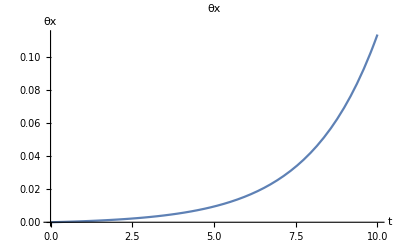

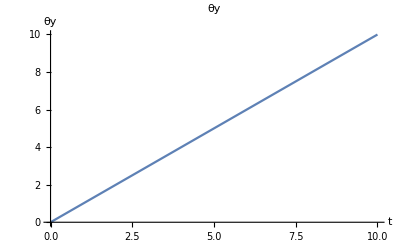

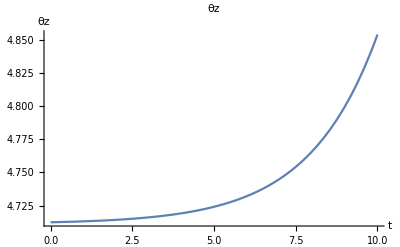

```mathematica
m=1;xd=1;yd=2;zd=3;Ix=(1/12)*m*(yd^2+zd^2);
Iy=(1/12)*m*(zd^2+xd^2);Iz=(1/12)*m*(xd^2+yd^2);
(*Intermediate Axis of Inertia is Iy*)
(*If rotation about Ix and Iz is perterbed slightly, the rotation is still stable, but if rotation about Iy is perterbed slightly, it will go unstable*)

(*Principle Axis of Intermediate Inertia Animation: Iy*)
soln=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==0.0005,Derivative[1][θy][0]==1,Derivative[1][θz][0]==0.0005},{θx,θy,θz},{t,0,80}]

ax[t_]:=Evaluate[θx[t]/.soln[[1,1]]]
ay[t_]:=Evaluate[θy[t]/.soln[[1,2]]]
az[t_]:=Evaluate[θz[t]/.soln[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax[t],{1,0,0}],ay[t],{0,1,0}],az[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principle Axis of Intermediate Inertia Animation: Unstable Rotation"],{t,0,80}, AnimationRate->1]

Plot[Evaluate[θx[t]/.soln[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]
```

## Rotation about Axis of Maximum Inertia (Using Euler Equations):

{{θx→InterpolatingFunction[{{0., 30.}}, <>],θy→InterpolatingFunction[{{0., 30.}}, <>],θz→InterpolatingFunction[{{0., 30.}}, <>]}}

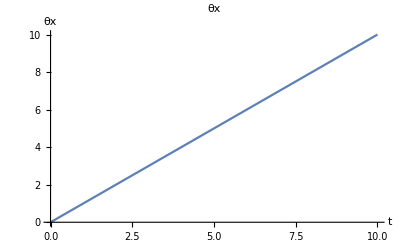

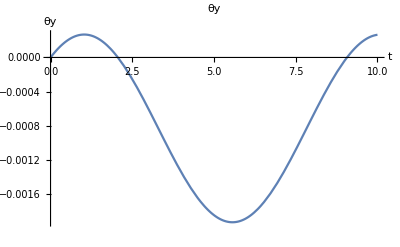

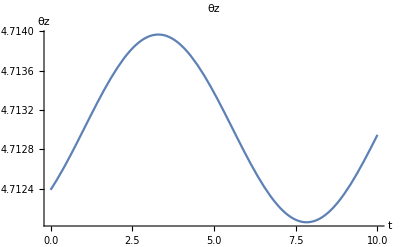

```mathematica
(*Principle Axis of Maximum Inertia Animation: Ix*)
soln2=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==1,Derivative[1][θy][0]==0.0005,Derivative[1][θz][0]==0.0005},{θx,θy,θz},{t,0,30}]

ax2[t_]:=Evaluate[θx[t]/.soln2[[1,1]]]
ay2[t_]:=Evaluate[θy[t]/.soln2[[1,2]]]
az2[t_]:=Evaluate[θz[t]/.soln2[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax2[t],{1,0,0}],ay2[t],{0,1,0}],az2[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principal Axis of Maximum Inertia Animation: Stable Rotation"],{t,0,30}]

Plot[Evaluate[θx[t]/.soln2[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln2[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln2[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]
```

## Rotation about Axis of Minimum Inertia (Using Euler Equations):

{{θx→InterpolatingFunction[{{0., 30.}}, <>],θy→InterpolatingFunction[{{0., 30.}}, <>],θz→InterpolatingFunction[{{0., 30.}}, <>]}}

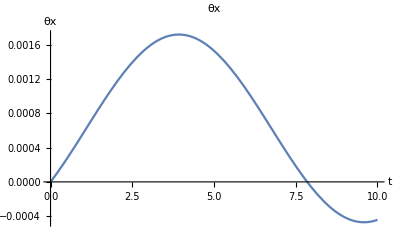

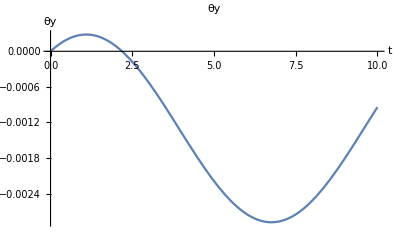

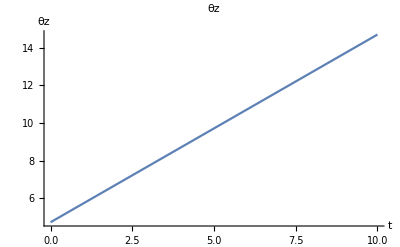

```mathematica
(*Principle Axis of Minimum Inertia Animation: Iz*)
soln3=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==0.0005,Derivative[1][θy][0]==0.0005,Derivative[1][θz][0]==1},{θx,θy,θz},{t,0,30}]

ax3[t_]:=Evaluate[θx[t]/.soln3[[1,1]]]
ay3[t_]:=Evaluate[θy[t]/.soln3[[1,2]]]
az3[t_]:=Evaluate[θz[t]/.soln3[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax3[t],{1,0,0}],ay3[t],{0,1,0}],az3[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel-> "Principal Axis of Minimum Inertia Animation: Stable Rotation"],{t,0,30}]

Plot[Evaluate[θx[t]/.soln3[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln3[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln3[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]
```

### These are the equations I used to find which impact condition to use. I choose the impact that happened first, and used the time for first impact in the impact update laws. To make the meat of the code nicer, I took them out. I would like to write code that will check this for me, but for now the purpose of this project the manual labour will suffice.

```mathematica
q={{ψ[t]},{ϕ[t]},{θ[t]}};
(*FIRST AND SECOND TIME DERIVATIVES: *)
dq = D[q, t];
ddq = D[dq, t];

(*ROTATION ABOUT X AXIS: *)
ωx = {1,0,0};
Rx = RotationMatrix[ψ[t], ωx];

(*ROTATION ABOUT Y AXIS: *)
ωy = {0,1,0};
Ry = RotationMatrix[ϕ[t], ωy];

(*ROTATION ABOUT Z AXIS: *)
ωz = {0,0,1};
Rz = RotationMatrix[θ[t], ωz];

R = Rx.Ry.Rz;

p = {{0},{0},{0}};
Twb = Join[Join[Rᵀ,pᵀ]ᵀ, {{0,0,0,1}}];
Twbdot = D[Twb, t];

Tbw = InverseTransformMatrix[Twb];

(*BODY VELOCITIES: *)
V= UnHat3D[Inverse[Twb].Twbdot];

(*Intertia Tensors*)
rb={{x},{y},{z}};
rhat = Hat[rb];
ℐ =∫_(-zd/2)^(zd/2) ∫_(-yd/2)^(yd/2) ∫_(-xd/2)^(xd/2) ρ*( rhat)ᵀ.( rhat )ⅆxⅆyⅆz;

G = Join[Join[m*IdentityMatrix[3],ConstantArray[0,{3,3}]]ᵀ, Join[ConstantArray[0,{3,3}],ℐ]ᵀ];

(*KINETIC ENERGY: *)
KE = 1/2*Vᵀ.G.V;

(*TODO::: FIX INERTIAL FRAME: *)
CM =  {{0},{0},{0}};
rW = NonHomogenize[Twb.Homogenize[CM]];

(*POTENTIAL ENERGY: *)
PE = m*g*rW[[3]];

(*LAGRANGIAN: *)
Lag = KE - PE//FullSimplify;
(*Generalized momentum*)
p = D[Lag, dqᵀ];

(*Hamiltonian*)
TotalEnergy = KE + PE;
Ham = p.dq-Lag;

(*EULER LAGRANGE EQUATIONS: *)
Eq1 = D[D[Lag, dq[[1]]],t]-D[Lag, q[[1]]] ==0;
Eq2 = D[D[Lag, dq[[2]]],t]-D[Lag, q[[2]]] ==0;
Eq3 = D[D[Lag, dq[[3]]],t]-D[Lag, q[[3]]] == 0;

(*FIND EQUTIONS OF MOTION: *)
ELtemp = Solve[Eq1&& Eq2 && Eq3,Flatten[{ddq}]];

(*PARAMETERS: *)
m=10;xd=1;yd=2;zd=3;g=9.81;ρ = 3;

(*INITIAL CONDITIONS: *)
InitCon= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.005,
Derivative[1][ϕ][0]==1,
Derivative[1][θ][0]==0.005};

(*IMPACTS: *)
(*Point of Impact in Space: *)
pw={{-xd/2},{yd/2+yd/4},{zd/2}};
pb=Tbw.Homogenize[pw];

(*IMPACT CONDITIONS: *)
phi1impact=pb[[1]]-xd/2;
phi2impact=pb[[1]]+xd/2;
phi3impact = pb[[2]]-yd/2;
phi4impact = pb[[2]] +yd/2;
phi5impact = pb[[3]]-zd/2;
phi6impact = pb[[3]]+zd/2;

gradphi1impact = D[phi1impact,qᵀ];
gradphi2impact = D[phi2impact,qᵀ];
gradphi3impact = D[phi3impact,qᵀ];
gradphi4impact = D[phi4impact,qᵀ];
gradphi5impact = D[phi5impact,qᵀ];
gradphi6impact = D[phi6impact,qᵀ];

EL={ψ''[t]==ELtemp[[1,1,2]],ϕ''[t]==ELtemp[[1,2,2]],θ''[t]==ELtemp[[1,3,2]]};
tmax = 10;

(*finding first impact phi*)
Imptest1 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi1impact }];
Imptest2 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi2impact }];
Imptest3 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi3impact }];
Imptest4 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi4impact }];
Imptest5 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi5impact }];
Imptest6 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi6impact }];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["First Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol1 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi4impact }];
tmax1 = InterpolatingFunctionDomain[First[ψ/.Impsol1]][[1,-1]];

(*FINDING FIRST IMPACT :*)
(****************************************************************************************)
Impsol1 = NDSolve[Join[EL, InitCon],{ψ,ϕ,θ}, {t, 0, tmax}, Method->{"EventLocator","Event"-> phi4impact }];
tmax1 = InterpolatingFunctionDomain[First[ψ/.Impsol1]][[1,-1]];

(*Conditions right before impact tminus*)
Hamminus = Ham/.t-> tminus;
Hamold1 = ((Hamminus/.tminus-> tmax1)/.Impsol1)[[1]];
Hamplus1 = (Ham/.t-> tplus)/.{ψ[tplus]-> (ψ[tmax1]/.Impsol1)[[1]], ϕ[tplus]-> (ϕ[tmax1]/.Impsol1)[[1]],θ[tplus]-> (θ[tmax1]/.Impsol1)[[1]]};

pminus = p/.t-> tminus;
pold = ((pminus/.tminus-> tmax1)/.Impsol1)[[1]]//FullSimplify;
pplus = (p/.t-> tplus)/.{ψ[tplus]-> (ψ[tmax1]/.Impsol1)[[1]], ϕ[tplus]-> (ϕ[tmax1]/.Impsol1)[[1]],θ[tplus]-> (θ[tmax1]/.Impsol1)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi4impact =(( gradphi4impact/.t->  tmax1)/.Impsol1)[[1]];
qprimupdate = Solve[Hamplus1-Hamold1 == 0 && pplus-pold== λ*{gradphi4impact},Flatten[{ψ'[tplus],ϕ'[tplus],θ'[tplus],λ}]];
(****************************************************************************************)

(*finding second impact phi*)
tmax2 =10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Second Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];


Impsol2=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol1)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol1)[[1]],θ''[t]==(θ''[t]/.Impsol1)[[1]],ψ[tmax1]==(ψ[tmax1]/.Impsol1)[[1]],ϕ[tmax1]==(ϕ[tmax1]/.Impsol1)[[1]],θ[tmax1]==(θ[tmax1]/.Impsol1)[[1]],ψ'[tmax1]==(ψ'[tplus]/.qprimupdate[[2,1]]),ϕ'[tmax1]==(ϕ'[tplus]/.qprimupdate[[2,2]]),θ'[tmax1]==(θ'[tplus]/.qprimupdate[[2,3]])},{ψ,ϕ,θ},{t,tmax1,tmax2},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax2 = InterpolatingFunctionDomain[First[ψ/.Impsol2]][[1,-1]];

Hamminus = Ham/.t-> tminus2;
Hamold2 = ((Hamminus/.tminus2-> tmax2)/.Impsol2)[[1]];
Hamplus2 = (Ham/.t-> tplus2)/.{ψ[tplus2]-> (ψ[tmax2]/.Impsol2)[[1]], ϕ[tplus2]-> (ϕ[tmax2]/.Impsol2)[[1]],θ[tplus2]-> (θ[tmax2]/.Impsol2)[[1]]};

pminus = p/.t-> tminus2;
pold = ((pminus/.tminus2-> tmax2)/.Impsol2)[[1]]//FullSimplify;
pplus = (p/.t-> tplus2)/.{ψ[tplus2]-> (ψ[tmax2]/.Impsol2)[[1]], ϕ[tplus2]-> (ϕ[tmax2]/.Impsol2)[[1]],θ[tplus2]-> (θ[tmax2]/.Impsol2)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax2)/.Impsol2)[[1]];
qprimupdate2 = Solve[Hamplus2-Hamold2 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus2],ϕ'[tplus2],θ'[tplus2],λ}]];


(*finding third impact phi: *)
tmax3 =10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[2,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[2,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Third Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];


Impsol3=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol2)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol2)[[1]],θ''[t]==(θ''[t]/.Impsol2)[[1]],ψ[tmax2]==(ψ[tmax2]/.Impsol2)[[1]],ϕ[tmax2]==(ϕ[tmax2]/.Impsol2)[[1]],θ[tmax2]==(θ[tmax2]/.Impsol2)[[1]],ψ'[tmax2]==(ψ'[tplus2]/.qprimupdate2[[1,1]]),ϕ'[tmax2]==(ϕ'[tplus2]/.qprimupdate2[[1,2]]),θ'[tmax2]==(θ'[tplus2]/.qprimupdate2[[1,3]])},{ψ,ϕ,θ},{t,tmax2,tmax3},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax3 = InterpolatingFunctionDomain[First[ψ/.Impsol3]][[1,-1]];

Hamminus = Ham/.t-> tminus3;
Hamold3 = ((Hamminus/.tminus3-> tmax3)/.Impsol3)[[1]];
Hamplus3 = (Ham/.t-> tplus3)/.{ψ[tplus3]-> (ψ[tmax3]/.Impsol3)[[1]], ϕ[tplus3]-> (ϕ[tmax3]/.Impsol3)[[1]],θ[tplus3]-> (θ[tmax3]/.Impsol3)[[1]]};

pminus = p/.t-> tminus3;
pold = ((pminus/.tminus3-> tmax3)/.Impsol3)[[1]]//FullSimplify;
pplus = (p/.t-> tplus3)/.{ψ[tplus3]-> (ψ[tmax3]/.Impsol3)[[1]], ϕ[tplus3]-> (ϕ[tmax3]/.Impsol3)[[1]],θ[tplus3]-> (θ[tmax3]/.Impsol3)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax3)/.Impsol3)[[1]];
qprimupdate3 = Solve[Hamplus3-Hamold3 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus3],ϕ'[tplus3],θ'[tplus3],λ}]];

(**FINDING FOR TMAX 4**)

tmax4 =10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Fourth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol4=
NDSolve[{ψ''[t]==(ψ''[t]/.Impsol3)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol3)[[1]],θ''[t]==(θ''[t]/.Impsol3)[[1]],ψ[tmax3]==(ψ[tmax3]/.Impsol3)[[1]],ϕ[tmax3]==(ϕ[tmax3]/.Impsol3)[[1]],θ[tmax3]==(θ[tmax3]/.Impsol3)[[1]],ψ'[tmax3]==(ψ'[tplus3]/.qprimupdate3[[1,1]]),ϕ'[tmax3]==(ϕ'[tplus3]/.qprimupdate3[[1,2]]),θ'[tmax3]==(θ'[tplus3]/.qprimupdate3[[1,3]])},{ψ,ϕ,θ},{t,tmax3,tmax4},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax4 = InterpolatingFunctionDomain[First[ψ/.Impsol4]][[1,-1]];

Hamminus = Ham/.t-> tminus4;
Hamold4 = ((Hamminus/.tminus4-> tmax4)/.Impsol4)[[1]];
Hamplus4 = (Ham/.t-> tplus4)/.{ψ[tplus4]-> (ψ[tmax4]/.Impsol4)[[1]], ϕ[tplus4]-> (ϕ[tmax4]/.Impsol4)[[1]],θ[tplus4]-> (θ[tmax4]/.Impsol4)[[1]]};

pminus = p/.t-> tminus4;
pold = ((pminus/.tminus4-> tmax4)/.Impsol4)[[1]]//FullSimplify;
pplus = (p/.t-> tplus4)/.{ψ[tplus4]-> (ψ[tmax4]/.Impsol4)[[1]], ϕ[tplus4]-> (ϕ[tmax4]/.Impsol4)[[1]],θ[tplus4]-> (θ[tmax4]/.Impsol4)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax4)/.Impsol4)[[1]];
qprimupdate4 = Solve[Hamplus4-Hamold4 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus4],ϕ'[tplus4],θ'[tplus4],λ}]];

(**FINDING FOR TMAX5 :***)
tmax5 =10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[2,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[2,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[2,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Fifth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];


Impsol5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol4)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol4)[[1]],θ''[t]==(θ''[t]/.Impsol4)[[1]],ψ[tmax4]==(ψ[tmax4]/.Impsol4)[[1]],ϕ[tmax4]==(ϕ[tmax4]/.Impsol4)[[1]],θ[tmax4]==(θ[tmax4]/.Impsol4)[[1]],ψ'[tmax4]==(ψ'[tplus4]/.qprimupdate4[[1,1]]),ϕ'[tmax4]==(ϕ'[tplus4]/.qprimupdate4[[1,2]]),θ'[tmax4]==(θ'[tplus4]/.qprimupdate4[[1,3]])},{ψ,ϕ,θ},{t,tmax4,tmax5},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax5 = InterpolatingFunctionDomain[First[ψ/.Impsol5]][[-1,1]];

Hamminus = Ham/.t-> tminus5;
Hamold5 = ((Hamminus/.tminus5-> tmax5)/.Impsol5)[[1]];
Hamplus5 = (Ham/.t-> tplus5)/.{ψ[tplus5]-> (ψ[tmax5]/.Impsol5)[[1]], ϕ[tplus5]-> (ϕ[tmax5]/.Impsol5)[[1]],θ[tplus5]-> (θ[tmax5]/.Impsol5)[[1]]};

pminus = p/.t-> tminus5;
pold = ((pminus/.tminus5-> tmax5)/.Impsol5)[[1]]//FullSimplify;
pplus = (p/.t-> tplus5)/.{ψ[tplus5]-> (ψ[tmax5]/.Impsol5)[[1]], ϕ[tplus5]-> (ϕ[tmax5]/.Impsol5)[[1]],θ[tplus5]-> (θ[tmax5]/.Impsol5)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax5)/.Impsol5)[[1]];
qprimupdate5 = Solve[Hamplus5-Hamold5 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus5],ϕ'[tplus5],θ'[tplus5],λ}]];

(*Testing for tmax 6: *)
tmax6 =10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Sixth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol6=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol5)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol5)[[1]],θ''[t]==(θ''[t]/.Impsol5)[[1]],ψ[tmax5]==(ψ[tmax5]/.Impsol5)[[1]],ϕ[tmax5]==(ϕ[tmax5]/.Impsol5)[[1]],θ[tmax5]==(θ[tmax5]/.Impsol5)[[1]],ψ'[tmax5]==(ψ'[tplus5]/.qprimupdate5[[1,1]]),ϕ'[tmax5]==(ϕ'[tplus5]/.qprimupdate5[[1,2]]),θ'[tmax5]==(θ'[tplus5]/.qprimupdate5[[1,3]])},{ψ,ϕ,θ},{t,tmax5,tmax6},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax6 = InterpolatingFunctionDomain[First[ψ/.Impsol6]][[1,-1]];

Hamminus = Ham/.t-> tminus6;
Hamold6 = ((Hamminus/.tminus6-> tmax6)/.Impsol6)[[1]];
Hamplus6 = (Ham/.t-> tplus6)/.{ψ[tplus6]-> (ψ[tmax6]/.Impsol6)[[1]], ϕ[tplus6]-> (ϕ[tmax6]/.Impsol6)[[1]],θ[tplus6]-> (θ[tmax6]/.Impsol6)[[1]]};

pminus = p/.t-> tminus6;
pold = ((pminus/.tminus6-> tmax6)/.Impsol6)[[1]]//FullSimplify;
pplus = (p/.t-> tplus6)/.{ψ[tplus6]-> (ψ[tmax6]/.Impsol6)[[1]], ϕ[tplus6]-> (ϕ[tmax6]/.Impsol6)[[1]],θ[tplus6]-> (θ[tmax6]/.Impsol6)[[1]]};


(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax6)/.Impsol6)[[1]];
qprimupdate6 = Solve[Hamplus6-Hamold6 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus6],ϕ'[tplus6],θ'[tplus6],λ}]];

(**testing for tmax 7: **)
tmax7=10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[1,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[1,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[1,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Seventh Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];


Impsol7=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol6)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol6)[[1]],θ''[t]==(θ''[t]/.Impsol6)[[1]],ψ[tmax6]==(ψ[tmax6]/.Impsol6)[[1]],ϕ[tmax6]==(ϕ[tmax6]/.Impsol6)[[1]],θ[tmax6]==(θ[tmax6]/.Impsol6)[[1]],ψ'[tmax6]==(ψ'[tplus6]/.qprimupdate6[[2,1]]),ϕ'[tmax6]==(ϕ'[tplus6]/.qprimupdate6[[2,2]]),θ'[tmax6]==(θ'[tplus6]/.qprimupdate6[[2,3]])},{ψ,ϕ,θ},{t,tmax6,tmax7},Method->{"EventLocator","Event"-> (phi1impact)}];
tmax7 = InterpolatingFunctionDomain[First[ψ/.Impsol7]][[1,-1]];

Hamminus = Ham/.t-> tminus7;
Hamold7 = ((Hamminus/.tminus7-> tmax7)/.Impsol7)[[1]];
Hamplus7 = (Ham/.t-> tplus7)/.{ψ[tplus7]-> (ψ[tmax7]/.Impsol7)[[1]], ϕ[tplus7]-> (ϕ[tmax7]/.Impsol7)[[1]],θ[tplus7]-> (θ[tmax7]/.Impsol7)[[1]]};

pminus = p/.t-> tminus7;
pold = ((pminus/.tminus7-> tmax7)/.Impsol7)[[1]]//FullSimplify;
pplus = (p/.t-> tplus7)/.{ψ[tplus7]-> (ψ[tmax7]/.Impsol7)[[1]], ϕ[tplus7]-> (ϕ[tmax7]/.Impsol7)[[1]],θ[tplus7]-> (θ[tmax7]/.Impsol7)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax7)/.Impsol7)[[1]];
qprimupdate7 = Solve[Hamplus7-Hamold7 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus7],ϕ'[tplus7],θ'[tplus7],λ}]];

(*testing for tmax8: *)
tmax8=10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Eighth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol8=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol7)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol7)[[1]],θ''[t]==(θ''[t]/.Impsol7)[[1]],ψ[tmax7]==(ψ[tmax7]/.Impsol7)[[1]],ϕ[tmax7]==(ϕ[tmax7]/.Impsol7)[[1]],θ[tmax7]==(θ[tmax7]/.Impsol7)[[1]],ψ'[tmax7]==(ψ'[tplus7]/.qprimupdate7[[2,1]]),ϕ'[tmax7]==(ϕ'[tplus7]/.qprimupdate7[[2,2]]),θ'[tmax7]==(θ'[tplus7]/.qprimupdate7[[2,3]])},{ψ,ϕ,θ},{t,tmax7,tmax8},Method->{"EventLocator","Event"-> (phi2impact)}];

tmax8 = InterpolatingFunctionDomain[First[ψ/.Impsol8]][[1,-1]];

Hamminus = Ham/.t-> tminus8;
Hamold8 = ((Hamminus/.tminus8-> tmax8)/.Impsol8)[[1]];
Hamplus8 = (Ham/.t-> tplus8)/.{ψ[tplus8]-> (ψ[tmax8]/.Impsol8)[[1]], ϕ[tplus8]-> (ϕ[tmax8]/.Impsol8)[[1]],θ[tplus8]-> (θ[tmax8]/.Impsol8)[[1]]};

pminus = p/.t-> tminus8;
pold = ((pminus/.tminus8-> tmax8)/.Impsol8)[[1]]//FullSimplify;
pplus = (p/.t-> tplus8)/.{ψ[tplus8]-> (ψ[tmax8]/.Impsol8)[[1]], ϕ[tplus8]-> (ϕ[tmax8]/.Impsol8)[[1]],θ[tplus8]-> (θ[tmax8]/.Impsol8)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi2impact =(( gradphi2impact/.t->  tmax8)/.Impsol8)[[1]];
qprimupdate8 = Solve[Hamplus8-Hamold8 == 0 && pplus-pold== λ*{gradphi2impact},Flatten[{ψ'[tplus8],ϕ'[tplus8],θ'[tplus8],λ}]];

(*Finding for tmax9: *)
tmax9=10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];


Print["Ninth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol9=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol8)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol8)[[1]],θ''[t]==(θ''[t]/.Impsol8)[[1]],ψ[tmax8]==(ψ[tmax8]/.Impsol8)[[1]],ϕ[tmax8]==(ϕ[tmax8]/.Impsol8)[[1]],θ[tmax8]==(θ[tmax8]/.Impsol8)[[1]],ψ'[tmax8]==(ψ'[tplus8]/.qprimupdate8[[2,1]]),ϕ'[tmax8]==(ϕ'[tplus8]/.qprimupdate8[[2,2]]),θ'[tmax8]==(θ'[tplus8]/.qprimupdate8[[2,3]])},{ψ,ϕ,θ},{t,tmax8,tmax9},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax9 = InterpolatingFunctionDomain[First[ψ/.Impsol9]][[1,-1]];

Hamminus = Ham/.t-> tminus9;
Hamold9 = ((Hamminus/.tminus9-> tmax9)/.Impsol9)[[1]];
Hamplus9 = (Ham/.t-> tplus9)/.{ψ[tplus9]-> (ψ[tmax9]/.Impsol9)[[1]], ϕ[tplus9]-> (ϕ[tmax9]/.Impsol9)[[1]],θ[tplus9]-> (θ[tmax9]/.Impsol9)[[1]]};

pminus = p/.t-> tminus9;
pold = ((pminus/.tminus9-> tmax9)/.Impsol9)[[1]]//FullSimplify;
pplus = (p/.t-> tplus9)/.{ψ[tplus9]-> (ψ[tmax9]/.Impsol9)[[1]], ϕ[tplus9]-> (ϕ[tmax9]/.Impsol9)[[1]],θ[tplus9]-> (θ[tmax9]/.Impsol9)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax9)/.Impsol9)[[1]];
qprimupdate9 = Solve[Hamplus9-Hamold9 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus9],ϕ'[tplus9],θ'[tplus9],λ}]];

(*Testing for tenth: *)
tmax10=10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Tenth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol10=NDSolve[{ψ''[t]==(ψ''[t]/.Impsol9)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol9)[[1]],θ''[t]==(θ''[t]/.Impsol9)[[1]],ψ[tmax9]==(ψ[tmax9]/.Impsol9)[[1]],ϕ[tmax9]==(ϕ[tmax9]/.Impsol9)[[1]],θ[tmax9]==(θ[tmax9]/.Impsol9)[[1]],ψ'[tmax9]==(ψ'[tplus9]/.qprimupdate9[[1,1]]),ϕ'[tmax9]==(ϕ'[tplus9]/.qprimupdate9[[1,2]]),θ'[tmax9]==(θ'[tplus9]/.qprimupdate9[[1,3]])},{ψ,ϕ,θ},{t,tmax9,tmax10},Method->{"EventLocator","Event"-> (phi1impact)}];

tmax10 = InterpolatingFunctionDomain[First[ψ/.Impsol10]][[1,-1]];

Hamminus = Ham/.t-> tminus10;
Hamold10 = ((Hamminus/.tminus10-> tmax10)/.Impsol10)[[1]];
Hamplus10 = (Ham/.t-> tplus10)/.{ψ[tplus10]-> (ψ[tmax10]/.Impsol10)[[1]], ϕ[tplus10]-> (ϕ[tmax10]/.Impsol10)[[1]],θ[tplus10]-> (θ[tmax10]/.Impsol10)[[1]]};

pminus = p/.t-> tminus10;
pold = ((pminus/.tminus10-> tmax10)/.Impsol10)[[1]]//FullSimplify;
pplus = (p/.t-> tplus10)/.{ψ[tplus10]-> (ψ[tmax10]/.Impsol10)[[1]], ϕ[tplus10]-> (ϕ[tmax10]/.Impsol10)[[1]],θ[tplus10]-> (θ[tmax10]/.Impsol10)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi1impact =(( gradphi1impact/.t->  tmax10)/.Impsol10)[[1]];
qprimupdate10 = Solve[Hamplus10-Hamold10 == 0 && pplus-pold== λ*{gradphi1impact},Flatten[{ψ'[tplus10],ϕ'[tplus10],θ'[tplus10],λ}]];

(*finding for tmax11: *)
tmax11=10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[1,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[1,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[1,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];


Print["Elevinth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol11= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol10)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol10)[[1]],θ''[t]==(θ''[t]/.Impsol10)[[1]],ψ[tmax10]==(ψ[tmax10]/.Impsol10)[[1]],ϕ[tmax10]==(ϕ[tmax10]/.Impsol10)[[1]],θ[tmax10]==(θ[tmax10]/.Impsol10)[[1]],ψ'[tmax10]==(ψ'[tplus10]/.qprimupdate10[[2,1]]),ϕ'[tmax10]==(ϕ'[tplus10]/.qprimupdate10[[2,2]]),θ'[tmax10]==(θ'[tplus10]/.qprimupdate10[[2,3]])},{ψ,ϕ,θ},{t,tmax10,tmax11},Method->{"EventLocator","Event"-> (phi6impact)}];

tmax11 = InterpolatingFunctionDomain[First[ψ/.Impsol11]][[1,-1]];

Hamminus = Ham/.t-> tminus11;
Hamold11 = ((Hamminus/.tminus11-> tmax11)/.Impsol11)[[1]];
Hamplus11= (Ham/.t-> tplus11)/.{ψ[tplus11]-> (ψ[tmax11]/.Impsol11)[[1]], ϕ[tplus11]-> (ϕ[tmax11]/.Impsol11)[[1]],θ[tplus11]-> (θ[tmax11]/.Impsol11)[[1]]};

pminus = p/.t-> tminus11;
pold = ((pminus/.tminus11-> tmax11)/.Impsol11)[[1]]//FullSimplify;
pplus = (p/.t-> tplus11)/.{ψ[tplus11]-> (ψ[tmax11]/.Impsol11)[[1]], ϕ[tplus11]-> (ϕ[tmax11]/.Impsol11)[[1]],θ[tplus11]-> (θ[tmax11]/.Impsol11)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi6impact =(( gradphi6impact/.t->  tmax11)/.Impsol11)[[1]];
qprimupdate11 = Solve[Hamplus11-Hamold11 == 0 && pplus-pold== λ*{gradphi6impact},Flatten[{ψ'[tplus11],ϕ'[tplus11],θ'[tplus11],λ}]];

(*Finding for the twelfth impact : *)
tmax12 = 10;
Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 = NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];

Print["Twelfth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];

Impsol12= NDSolve[{ψ''[t]==(ψ''[t]/.Impsol11)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol11)[[1]],θ''[t]==(θ''[t]/.Impsol11)[[1]],ψ[tmax11]==(ψ[tmax11]/.Impsol11)[[1]],ϕ[tmax11]==(ϕ[tmax11]/.Impsol11)[[1]],θ[tmax11]==(θ[tmax11]/.Impsol11)[[1]],ψ'[tmax11]==(ψ'[tplus11]/.qprimupdate11[[1,1]]),ϕ'[tmax11]==(ϕ'[tplus11]/.qprimupdate11[[1,2]]),θ'[tmax11]==(θ'[tplus11]/.qprimupdate11[[1,3]])},{ψ,ϕ,θ},{t,tmax11,tmax12},Method->{"EventLocator","Event"-> (phi3impact)}];

tmax12 = InterpolatingFunctionDomain[First[ψ/.Impsol12]][[1,-1]];

Hamminus = Ham/.t-> tminus12;
Hamold12 = ((Hamminus/.tminus12-> tmax12)/.Impsol12)[[1]];
Hamplus12 = (Ham/.t-> tplus12)/.{ψ[tplus12]-> (ψ[tmax12]/.Impsol12)[[1]], ϕ[tplus12]-> (ϕ[tmax12]/.Impsol12)[[1]],θ[tplus12]-> (θ[tmax12]/.Impsol12)[[1]]};

pminus = p/.t-> tminus12;
pold = ((pminus/.tminus12-> tmax12)/.Impsol12)[[1]]//FullSimplify;
pplus = (p/.t-> tplus12)/.{ψ[tplus12]-> (ψ[tmax12]/.Impsol12)[[1]], ϕ[tplus12]-> (ϕ[tmax12]/.Impsol12)[[1]],θ[tplus12]-> (θ[tmax12]/.Impsol12)[[1]]};

(*Solving for velocity right after impact tplus*)
gradphi3impact =(( gradphi3impact/.t->  tmax11)/.Impsol11)[[1]];
qprimupdate12 = Solve[Hamplus12-Hamold12 == 0 && pplus-pold== λ*{gradphi3impact},Flatten[{ψ'[tplus12],ϕ'[tplus12],θ'[tplus12],λ}]];

(*Finding thirteenth impact: *)
tmax13=10;Imptest1 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi1impact)}];
Imptest2 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi2impact)}];
Imptest3 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi3impact)}];
Imptest4 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi4impact)}];
Imptest5 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi5impact)}];
Imptest6 =NDSolve[{ψ''[t]==(ψ''[t]/.Impsol12)[[1]],ϕ''[t]==(ϕ''[t]/.Impsol12)[[1]],θ''[t]==(θ''[t]/.Impsol12)[[1]],ψ[tmax12]==(ψ[tmax12]/.Impsol12)[[1]],ϕ[tmax12]==(ϕ[tmax12]/.Impsol12)[[1]],θ[tmax12]==(θ[tmax12]/.Impsol12)[[1]],ψ'[tmax12]==(ψ'[tplus12]/.qprimupdate12[[2,1]]),ϕ'[tmax12]==(ϕ'[tplus12]/.qprimupdate12[[2,2]]),θ'[tmax12]==(θ'[tplus12]/.qprimupdate12[[2,3]])},{ψ,ϕ,θ},{t,tmax12,tmax13},Method->{"EventLocator","Event"-> (phi6impact)}];

time1 = InterpolatingFunctionDomain[First[ψ/.Imptest1]][[1,-1]];
time2 = InterpolatingFunctionDomain[First[ψ/.Imptest2]][[1,-1]];
time3 = InterpolatingFunctionDomain[First[ψ/.Imptest3]][[1,-1]];
time4 = InterpolatingFunctionDomain[First[ψ/.Imptest4]][[1,-1]];
time5 = InterpolatingFunctionDomain[First[ψ/.Imptest5]][[1,-1]];
time6 = InterpolatingFunctionDomain[First[ψ/.Imptest6]][[1,-1]];


Print["Thirtheenth Impact"];
Print["timephi11: ", time1];
Print["timephi2: ",  time2];
Print["timephi3: ", time3];
Print["timephi4: ", time4];
Print["timephi5: ", time5];
Print["timephi6: ", time6];
```

First Impact

timephi11: 10.

timephi2: 10.

timephi3: 3.49473

timephi4: 0.365568

timephi5: 5.62751

timephi6: 2.51708

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Second Impact

timephi11: 2.09929

timephi2: 1.36624

timephi3: 1.17768

timephi4: 3.1132

timephi5: 6.09515

timephi6: 1.57095

InterpolatingFunction::dmval: Input value TraditionalForm`{0.366316} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17774} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Third Impact

timephi11: 1.84112

timephi2: 1.41638

timephi3: 1.57977

timephi4: 1.65937

timephi5: 3.25298

timephi6: 3.20832

InterpolatingFunction::dmval: Input value TraditionalForm`{1.17773} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Fourth Impact

timephi11: 3.27346

timephi2: 3.22538

timephi3: 1.75234

timephi4: 2.32361

timephi5: 2.69984

timephi6: 1.95304

InterpolatingFunction::dmval: Input value TraditionalForm`{1.63314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Fifth Impact

timephi11: 2.66031

timephi2: 1.92646

timephi3: 1.99533

timephi4: 4.62906

timephi5: 6.22479

timephi6: 1.95071

InterpolatingFunction::dmval: Input value TraditionalForm`{1.75235} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Sixth Impact

timephi11: 3.14294

timephi2: 1.9955

timephi3: 1.87419

timephi4: 2.41024

timephi5: 2.3806

timephi6: 1.95304

InterpolatingFunction::dmval: Input value TraditionalForm`{2.17109} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Seventh Impact

timephi11: 3.27063

timephi2: 2.98924

timephi3: 2.73614

timephi4: 2.54825

timephi5: 9.99458

timephi6: 2.04084

InterpolatingFunction::dmval: Input value TraditionalForm`{1.99553} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Eighth Impact

timephi11: 2.38398

timephi2: 2.38351

timephi3: 2.38377

timephi4: 2.38358

timephi5: 2.55828

timephi6: 2.39172

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38342} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Ninth Impact

timephi11: 2.38398

timephi2: 2.38387

timephi3: 2.38377

timephi4: 2.38358

timephi5: 2.38355

timephi6: 2.38945

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38351} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Tenth Impact

timephi11: 2.38456

timephi2: 2.3846

timephi3: 2.3842

timephi4: 2.38476

timephi5: 8.09118

timephi6: 2.38729

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Elevinth Impact

timephi11: 2.38486

timephi2: 2.3846

timephi3: 2.38466

timephi4: 2.38476

timephi5: 2.38544

timephi6: 2.38522

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Twelfth Impact

timephi11: 2.38482

timephi2: 2.38488

timephi3: 2.38476

timephi4: 2.38563

timephi5: 2.38632

timephi6: 2.38494

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value TraditionalForm`{2.38476} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Thirtheenth Impact

timephi11: 2.38478

timephi2: 2.38479

timephi3: 2.38478

timephi4: 2.38479

timephi5: 2.38529

timephi6: 2.38479